### Fresnel and IOR

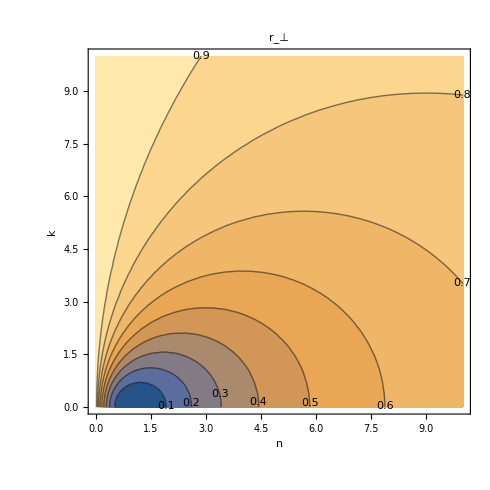
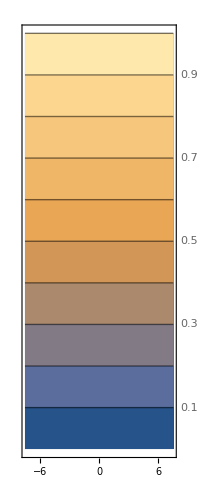
Here we’re attempting to study the paper “Artist Friendly Metallic Fresnel” (2014) Gubrandsen.

Gulbrandsen states that, accounting for the complex IOR (n,k), reflectance at normal incidence is given by:

r(n,k)=((n-1)^2+k^2)/((n+1)^2+k^2)

This gives the following graph:
-Graphics-       -Graphics-
If r is given as a color (the reflectance at normal incidence) then we can write:
k(r,n)=√(((n-1)^2-(r(n+1))^2)/(r-1))

k is valid only if r∈[0,1[ and n∈[(1+√r)/(1-√r),(1-√r)/(1+√r)]

### Applying to unpolarized Fresnel

Equations of polarized Fresnel reflectances are:

```mathematica
fortho[n_,k_,θ_]:=(n^2+k^2-2n Cos[θ]+Cos[θ]^2)/(n^2+k^2+2n Cos[θ]+Cos[θ]^2)
fpara[n_,k_,θ_]:=((n^2+k^2)Cos[θ]^2-2n Cos[θ]+1)/((n^2+k^2)Cos[θ]^2+2n Cos[θ]+1)
```

Unpolarized Fresnel is then given by:

```mathematica
R[n_,k_,θ_]:=(fortho[n,k,θ]+fpara[n,k,θ])/2
```

Or as a function of r and n :

```mathematica
k[r_,n_]:=√(((n-1)^2-r(n+1)^2)/(r-1));
R2[r_,n_,θ_]:=R[n,k [r,n],θ] (*(fortho[n,k[r,n],θ]+fpara[n,k[r,n],θ])/2*)
```

Plotting R as a function of n for a fixed r and θ:

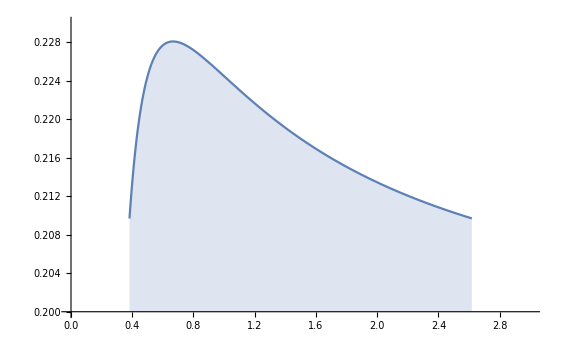

using parameter g to obtain IOR:

```mathematica
n[r_,g_]:=g *(1-r)/(1+r)+(1-g)*(1+√r)/(1-√r)
```

```mathematica
Manipulate[Plot[n[r,g],{r,0,1},PlotRange->{0,20}],{{g,0.2},0,1}]
```

So finally we have 2 expressions intuitively mapping (r,g) into (n,k).

```mathematica
R3[r_,g_,θ_]:=R2[r,n[r,g],θ];
```

# Generating a reflectance gradient

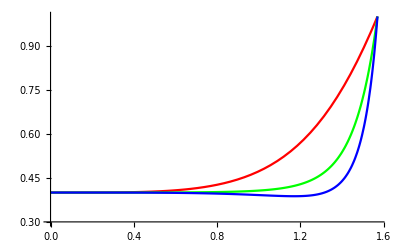

```mathematica
r={0.4,0.4,0.4};
g={1.0,0.5,0.0};
a=π/2;
Show[
Plot[R3[r[[1]],g[[1]],θ],{θ,0,a},PlotRange->{0.3,1},PlotStyle->Red],
Plot[R3[r[[2]],g[[2]],θ],{θ,0,a},PlotRange->{0.3,1},PlotStyle->Green],
Plot[R3[r[[3]],g[[3]],θ],{θ,0,a},PlotRange->{0.3,1},PlotStyle->Blue]
]
Gradient[
```

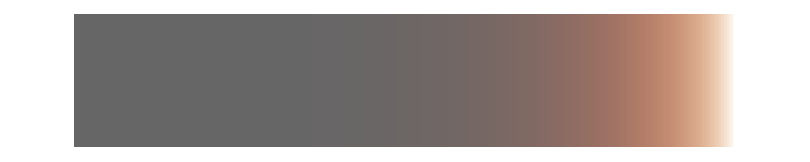

```mathematica
gradient=Table[{R3[r[[1]],g[[1]],θ], R3[r[[2]],g[[2]],θ], R3[r[[3]],g[[3]],θ]},{θ,0,π/2,π/2/255}];
rast = Table[gradient,{y,0,32}];
Graphics[Raster[rast]]
```

## Various Tests

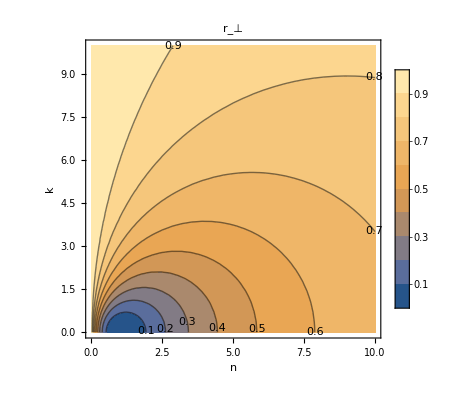

```mathematica
r[n_,k_]:=((n-1)^2+k^2)/((n+1)^2+k^2);
Plot3D[r[n,k],{n,0,10},{k,0,10}];
ContourPlot[r[n,k],{n,0,10},{k,0,10},PlotLegends->Automatic,ContourLabels->True,FrameLabel->Automatic,PlotLabel->"r_⊥"]
```

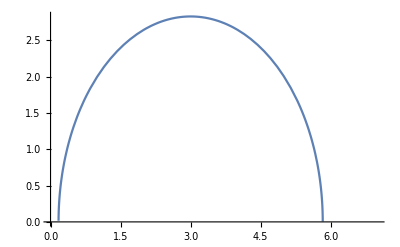

```mathematica
k[r_,n_]:=√(((n-1)^2-r(n+1)^2)/(r-1))
Plot[k[0.5,n],{n,0,7}]
```

```mathematica
ClampN[n_,r_]:=Max[(1-√r)/(1+√r),Min[(1+√r)/(1-√r),n]];
Manipulate[
Show[Plot[fortho[r,k[r,ClampN[n,r]],θ],{θ,0,π/2},PlotRange->{0,1}],
Plot[fpara[r,k[r,ClampN[n,r]],θ],{θ,0,π/2},PlotRange->{0,1}],
Plot[R[r,k[r,ClampN[n,r]],θ],{θ,0,π/2},PlotRange->{0,1},PlotStyle->Red]
],{{r,0.3},0,1},{{n,3.5},1,10}]
```

```mathematica
r=0.2;
Plot[R2[r,n,π/4],{n,0,3}, PlotRange->{0.20,0.230},Filling->Axis,RegionFunction->Function[{x},(1-√r)/(1+√r)< x <(1+√r)/(1-√r)]]
```

-Graphics-